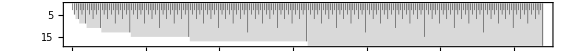

```mathematica
With[{haltingTimes=Table[Module[{t=0},NestWhile[(t++;TuringMachine[445,#])&,{{1,8,0},{IntegerDigits[n,2,8],0}},#[[1,3]]<=0&];t],{n,0,255}]},Graphics[{{GrayLevel[0.85],Table[Rectangle[{2^(i-1),-Max[Take[haltingTimes,{2^(i-1)+1,2^i}]]},{2^i,0}],{i,8}]},{AbsoluteThickness[.3],MapIndexed[Line[{{Last[#2]-.5,0},{Last[#2]-.5,-#1}}]&,haltingTimes]}},]]
```